Задание 3
Вычислить значение функций при заданном значении аргумента.
 a= th(1-π/2 i);
b=  e^(-1-2 π/3 i);

```mathematica
a=(Exp[1-π/2 I]-Exp[-1+π/2 I])/(Exp[1-π/2 I]+Exp[-1+π/2 I]);
a=(E(Cos[-π/2]+I Sin[-π/2])-E^-1(Cos[π/2]+I Sin[π/2]))/(E(Cos[-π/2]+I Sin[-π/2])+E^-1(Cos[π/2]+I Sin[π/2]));
a=(- E I-E^-1 I)/(- E I+E^-1 I);
```

```mathematica
a=(E +E^-1)/(E -E^-1)
```

```mathematica
a=Tanh[1]^-1
```

```mathematica
b=Exp[-1-2/3 π I];
b=E^-1(Cos[-2/3 π]+I Sin[-2/3 π])
```

(-1/2-(ⅈ √3)/2)/ⅇ

```mathematica
Otv={ReIm[a],ReIm[b]};
```

Изобразим полученный ответ:

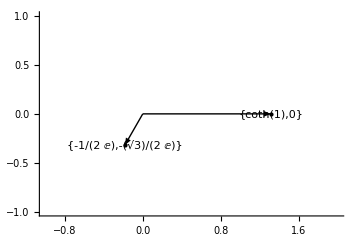

```mathematica
Show[Graphics[{Text[#,#,{#[[1]]-1,#[[2]]-1}],Arrow[{{0,0},#}],Point@#}&/@#,Axes->True,PlotRange->{{-1,2},{-1,1}}]&@Otv ]
```

Функция Graphics строит разные графические примитивы(текст, стрелка, оси).